# Result for massive ee->γγ

```mathematica
SetDirectory[NotebookDirectory[]];
matrixD=(m^2+(-1+T)T)^2*DiagonalMatrix[{1/m,1/m,1,1,1,1/m,1/m,1}]; (* Matrix from Eq.(2.34), necessary to obtain hard amplitudes *)
matrixG=<<"Glk"; (* This is Gram matrix in Eq.(2.30) *)
anum=1/137.03599*1/(4π);
```

This is Gram matrix in Eq.(2.30)

Notations: m=m_e/(√s), T=m^2-t/s, lmm=Log[m^2], log2ω_0=Log[(2 ω_0)/(√s)], ipi=I*π, Lbl=1 and nf=1 are flags.

## An example of a fast calculation

```mathematica
(* Load Hard amplitudes Eq.(2.35) and radiative corrections Eq.(3.2), (3.3)*)
Block[{Print=Null&},
{H0,H1,H2}=Get["Hkn/Hkn."<>ToString[#]]&/@Range[0,2];
Born=<<"deltas/Born";
delta1=<<"deltas/delta1";
delta2=<<"deltas/delta2";]
```

```mathematica
(* Multiply H from Eq.(2.35) by the inverse diagonal matrix D to obtain hard amplitudes *)
```

```mathematica
{ℋ0,ℋ1,ℋ2}=(Inverse[matrixD].Table[SeriesData[m,0,#[[invind]],0,Length[#[[invind]]],1],{invind,1,8}])&/@{H0,H1,H2};
```

```mathematica
(* Creating truncated series from coefficients for deltas*)
{delta1ser,delta2ser}=Normal@SeriesData[m,0,#,0,13,1]&/@{delta1,delta2};
```

```mathematica
(* Fast numerical calculation of hard amplitudes and Subscript[δ, 2] with power corrections, for example at ω0->0.1(√s)/2, T->3/7 and (√s)/Subscript[m, e]->4000 *)
```

```mathematica
{numℋ2,numδ2,numδ1}={Normal[ℋ2],anum^2 delta2ser,anum*delta1ser}/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/energy}/.ipi->I*π;
```

```mathematica
N[numℋ2/.T->3/7/.energy->4000]
```

{16.1123-16.0787 ⅈ,-0.0134023+0.0217147 ⅈ,2321.3-936.593 ⅈ,-2632.28+2066.83 ⅈ,1.3677-41.0065 ⅈ,785.799-760.405 ⅈ,15.3924-14.7036 ⅈ,-576.621+839.584 ⅈ}

```mathematica
N[numδ2/.T->3/7/.energy->4000]
```

0.00496786

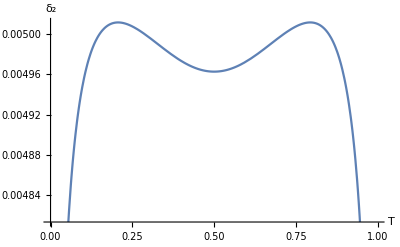

```mathematica
Plot[Evaluate[numδ2/.energy->4000],{T,10^-3,1-10^-3},PlotRange->Automatic,AxesLabel->{Style["T",Medium,Bold],Style["δ_2",Large,Medium]}]
```

## Obtaining the unpolarized differential cross section from hard amplitudes, see Eq.(2.36)

```mathematica
(* Load amplitudes from Eq.(2.35) *)
```

```mathematica
{H0,H1,H2}=Get["Hkn/Hkn."<>ToString[#]]&/@Range[0,2];
```

Born massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s).

One-loop hard massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s), lmm=Log[m^2], ipi=I*π.

Two-loop hard massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s), lmm=Log[m^2], ipi=I*π.
 nf=1 and Lbl=1 are flags.

```mathematica
(* Load W+2*Re(V) Eq.(2.20) and Gram matrix Eq.(2.30) *)
```

```mathematica
W2V=(<<"W2V"/.MZV[2]->Zeta[2]);
Glk=<<"Glk";
```

This is W+2*Re(V) for e^+e^-->2γ in Eq.(2.20)

This is Gram matrix in Eq.(2.30)

```mathematica
(* Calculating D^-1.G.D^-1 *)
```

```mathematica
DGD=Series[Simplify[Inverse[matrixD].Glk.Inverse[matrixD],Assumptions->m>0],{m,0,12}];
```

#### Calculating the hard amplitude squared

```mathematica
(* Creating truncated series from coefficients *)
```

```mathematica
{H2ser,H1ser,H0ser}=Table[SeriesData[m,0,#[[invind]],0,Length@(#[[invind]])+1,1],{invind,1,8}]&/@{H2,H1,H0};
```

```mathematica
(* two-loop a^2 terms: 2H0Re(H2) + Re(H1*H1) *)
```

```mathematica
twoborn=2H0ser.DGD.(H2ser/.ipi->0);
onesquared=H1ser.DGD.(H1ser/.ipi->-ipi);
```

```mathematica
Hsq2=MapAt[Collect[#,lmm|ipi|_PolyLog|_Log|_Zeta|π,Factor]&,(twoborn+onesquared),{3}]/.ipi^2->(-π^2);
```

```mathematica
(* one-loop a^1 terms: 2H0Re[H1] *)
```

```mathematica
oneborn=2H0ser.DGD.(H1ser/.ipi->0);
```

```mathematica
Hsq1=MapAt[Collect[#,lmm|ipi|_PolyLog|_Log|_Zeta|π,Factor]&,oneborn/.ipi^2->(-π^2),{3}];
```

```mathematica
(*Born a^0 terms: H0*H0 *)
```

```mathematica
bornsquared=H0ser.DGD.H0ser;
```

```mathematica
Hsq0=MapAt[Collect[#,lmm|ipi|_PolyLog|_Log|_Zeta|π,Factor]&,bornsquared,{3}];
```

#### Calculating a-series of exponent e^(a(W+2ReV))|H|^2

```mathematica
(* a^2 terms *)
```

```mathematica
Msq2=MapAt[Collect[#,lmm|_PolyLog|_Log|_Zeta|π,Factor]&,1/2*W2V^2*Hsq0+W2V*Hsq1+Hsq2,{3}];
```

```mathematica
(* a^1 terms *)
```

```mathematica
Msq1=MapAt[Collect[#,lmm|_PolyLog|_Log|_Zeta|π,Factor]&,W2V*Hsq0+Hsq1,{3}];
```

```mathematica
(* a^0 terms *)
```

```mathematica
Msq0=MapAt[Collect[#,lmm|_PolyLog|_Log|_Zeta|π,Factor]&,Hsq0,{3}];
```

#### Dividing on born cross section, obtaining δ_2 and δ_1

```mathematica
(* delta2ser and delta1ser have the format of truncated m-series. To obtain format as in Eq.(5.2) and (5.3) create Table of SeriesCoefficient  *)
```

```mathematica
delta1ser=Normal@MapAt[Collect[#,lmm|log2ω0|_PolyLog|_Log|_Zeta|π,Factor]&,Msq1/Msq0,{3}];
```

```mathematica
delta2ser=Normal@MapAt[Collect[#,lmm|log2ω0|_PolyLog|_Log|_Zeta|π,Factor]&,Msq2/Msq0,{3}];
```

```mathematica
N[anum^2*delta2ser/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/energy}/.T->3/7/.energy->4000]
```

0.00496786

## Creating Plots as in manuscript

```mathematica
Block[{Print=Null&},
Born=<<"deltas/Born";
delta1=<<"deltas/delta1";
delta2=<<"deltas/delta2";]
```

```mathematica
δ1trun=Normal@SeriesData[m,0,delta1,0,13,1];
δ2trun=Normal@SeriesData[m,0,delta2,0,13,1];
```

```mathematica
(* Defining  functions for Exact one-loop result Berends&Gastmans*)
```

```mathematica
deltav=-α/π(-1/2(2+(1+a^2)/a Log[b])lmm-(1+a^2)/a(Log[a]Log[b]-2PolyLog[2,-b]+1/2 PolyLog[2,b^2]+1/4 π^2)+g[k,τ]+g[τ,k])/.g[k_,τ_]:>1/(4(1/k+1/τ)^2-4(1/k+1/τ)-(k/τ+τ/k))((4/(k τ)(a(3-a^2))/((1-a^2)^2)+a)(1/2 Log[b]lmm-1/4(Log[b])^2-PolyLog[2,-b]-1/12 π^2)+Log[k]((1+a^2)/a(1/k-4/k^2+τ/(2k)+k/τ+1+4/(k τ)*a^2/(1-a^2))Log[b]+(1-a^2)/a((k-6)/(2τ))Log[b]+(3τ)/(2 k^2)(1+k)+3/τ+1-7/(k τ)+8/k-8/k^2-(τ^2-2k+k^2 τ)/(2 k^2 τ(k-1))-(2 k^2+τ)/(2τ(1-k)^2))+(1-a^2)/4(π^2-Log[b]^2)(2/k-(7k)/4-(3 k^2)/(4τ))+2/a(1/2-1/k)Log[b]+4(1/k+1/τ)^2-12/k-(3k)/(2τ)-(2k)/τ^2+1/(k-1)(k/τ+1/2)+2/k(π^2/6-PolyLog[2,1-k])(k^2/τ+τ/k^2+k/τ+k+τ/2+2/k-3/τ-1))/.{Log[k]->(Log[T]-lmm),Log[τ]->(Log[1-T]-lmm)};
deltas=-α/π((2+(1+a^2)/a Log[b])log2ω0+1/a Log[b]+(1+a^2)/a(PolyLog[2,(2a)/(1+a)]+1/4 Log[b]^2));
delta1exact=deltav+deltas/.α->1/137.03599/.{k->T/m^2,τ->(1-T)/m^2}/.b->(1-a)/(1+a)/.a->√(1-4 m^2);
```

```mathematica
SetOptions[Plot,GridLines->Automatic,LabelStyle->Directive[Black,Bold],AspectRatio->3/4,ImageSize->Large];
```

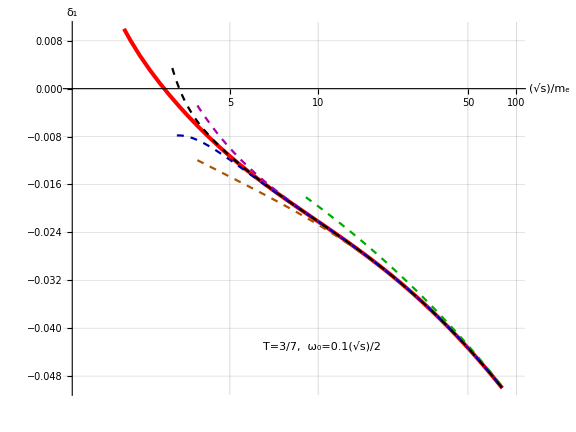

```mathematica
pl1=Plot[Evaluate[#1/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/x}/.T->3/7],{x,#2,200},PlotRange->{{1.9,100},{-0.05,0.01}},ScalingFunctions->{{Log[Log[#+1]]&,InverseFunction[Log[Log[#+1]]&]},None},PlotStyle->#3,AxesLabel->{Style["(√s)/m_e",Medium,Bold],Style["δ_1",Large,Medium]}]&@@@{{delta1exact,2,{Red,Thickness[0.005]}},{anum*delta1[[1]],9,{Darker[Green],Dashed}},{anum*Normal@Series[δ1trun,{m,0,2}],4,{Darker[Orange],Dashed}},{anum*Normal@Series[δ1trun,{m,0,4}],4,{Darker[Magenta],Dashed}},{anum*Normal@Series[δ1trun,{m,0,6}],3.5,{Darker[Blue],Dashed}},{anum*Normal@δ1trun,3.4,{Black,Dashed}}};
Show[pl1,Epilog->{Inset[Framed[Style["T=3/7,  ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.56, 0.13}]]}]
```

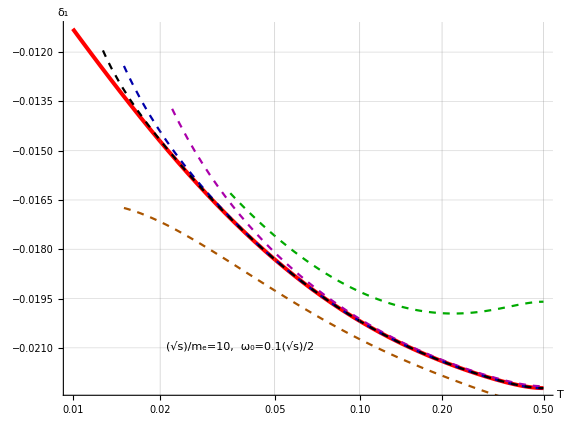

```mathematica
pl2=Plot[Evaluate[#1/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/x}/.x->10],{T,#2,1/2},PlotRange->Automatic,ScalingFunctions->{{Log[Log[#+1]]&,InverseFunction[Log[Log[#+1]]&]},None},PlotStyle->#3,AxesLabel->{Style["T",Medium,Bold],Style["δ_1",Large,Medium]}]&@@@{{delta1exact,10*10^-3,{Red,Thickness[0.005]}},{anum*delta1[[1]],35*10^-3,{Darker[Green],Dashed}},{anum*Normal@Series[δ1trun,{m,0,2}],15*10^-3,{Darker[Orange],Dashed}},{anum*Normal@Series[δ1trun,{m,0,4}],22*10^-3,{Darker[Magenta],Dashed}},{anum*Normal@Series[δ1trun,{m,0,6}],15*10^-3,{Darker[Blue],Dashed}},{anum*Normal@δ1trun,12.7*10^-3,{Black,Dashed}}};
Show[pl2,Epilog->{Inset[Framed[Style["(√s)/m_e=10,  ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.36, 0.13}]]}]
```

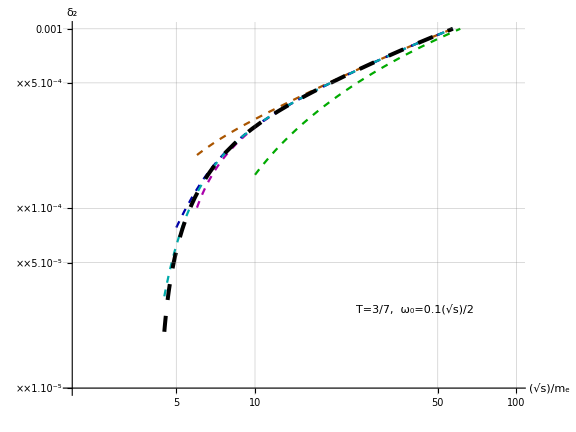

```mathematica
pl3=Plot[Evaluate[#1/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/x}/.T->3/7],{x,#2,200},PlotRange->{{2,100},{ 10^-5, 10^-3}},ScalingFunctions->{{Log[#]&,InverseFunction[Log[#]&]},{Log[#]&,InverseFunction[Log[#]&]}},PlotStyle->#3,AxesLabel->{Style["(√s)/m_e",Medium,Bold],Style["δ_2",Large,Medium]}]&@@@{{anum^2 delta2[[1]],10,{Darker[Green],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,2}],6,{Darker[Orange],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,4}],6,{Darker[Magenta],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,6}],5,{Darker[Blue],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,10}],4.5,{Darker[Cyan],Dashed}},{anum^2*Normal@δ2trun,4.5,{Black,Dashing[0.02],Thickness[0.005]}}};
Show[pl3,Epilog->{Inset[Framed[Style["T=3/7,  ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.76, 0.23}]]}]
```

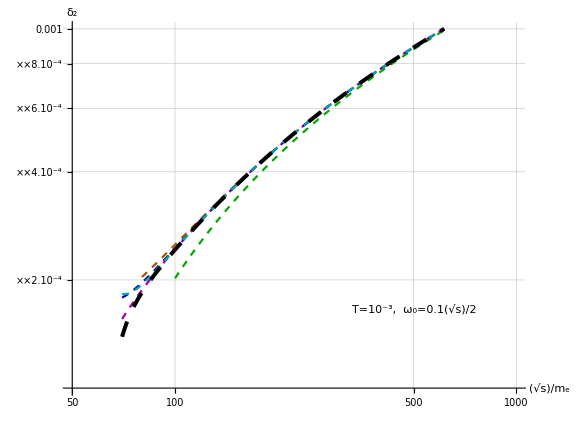

```mathematica
pl4=Plot[Evaluate[#1/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/x}/.T->10^-3],{x,#2,1000},PlotRange->{{50,1000},{ 10^-4,10^-3}},ScalingFunctions->{{Log[#]&,InverseFunction[Log[#]&]},{Log[#]&,InverseFunction[Log[#]&]}},PlotStyle->#3,AxesLabel->{Style["(√s)/m_e",Medium,Bold],Style["δ_2",Large,Medium]}]&@@@{{anum^2 delta2[[1]],100,{Darker[Green],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,2}],80,{Darker[Orange],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,4}],70,{Darker[Magenta],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,6}],70,{Darker[Blue],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,10}],70,{Darker[Cyan],Dashed}},{anum^2*Normal@δ2trun,70,{Black,Dashing[0.02],Thickness[0.005]}}};
Show[pl4,Epilog->{Inset[Framed[Style["T=10^-3,  ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.76, 0.23}]]}]
```

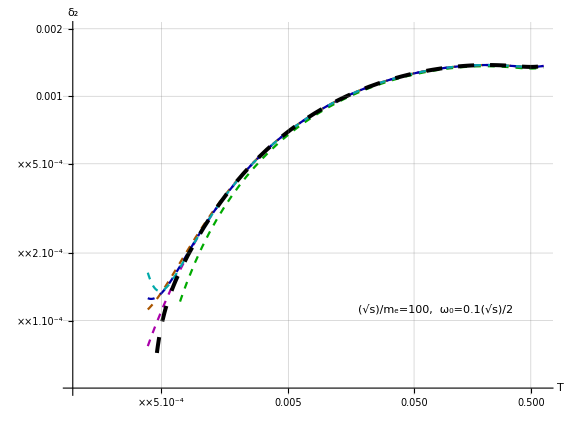

```mathematica
pl5=Plot[Evaluate[#1/.{nf->1,Lbl->1}/.{log2ω0->Log[(2ω0)/(√s)],lmm->Log[m^2]}/.{ω0->0.1(√s)/2,m->1/x}/.x->100],{T,#2,2/3},PlotRange->{{10^-4,2/3},{5 10^-5,2 10^-3}},ScalingFunctions->{{Log[Log[#+1]]&,InverseFunction[Log[Log[#+1]]&]},{Log[Log[#+1]]&,InverseFunction[Log[Log[#+1]]&]}},PlotStyle->#3,AxesLabel->{Style["T",Medium,Bold],Style["δ_2",Large,Medium]}]&@@@{{anum^2 delta2[[1]],7 10^-4,{Darker[Green],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,2}],3.9 10^-4,{Darker[Orange],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,4}],3.9 10^-4,{Darker[Magenta],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,6}],3.9 10^-4,{Darker[Blue],Dashed}},{anum^2*Normal@Series[δ2trun,{m,0,10}],3.9 10^-4,{Darker[Cyan],Dashed}},{anum^2*Normal@δ2trun,4.6 10^-4,{Black,Dashing[0.02],Thickness[0.005]}}};
Show[pl5,Epilog->{Inset[Framed[Style["(√s)/m_e=100,  ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.76, 0.23}]]}]
```

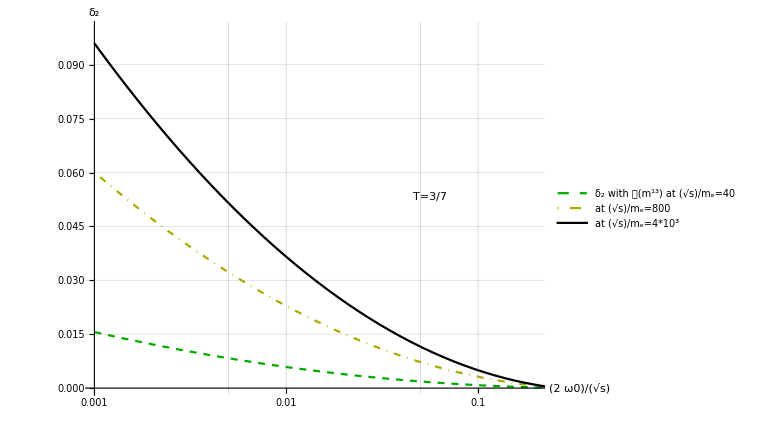

```mathematica
plomega=Plot[Evaluate[(anum^2*δ2trun/.{nf->1,Lbl->1}/.{log2ω0->Log[precision],lmm->Log[m^2]}/.{m->1/x}/.x->#)&/@{40,800,4000}/.T->3/7],{precision,10^-3,5 10^-1},PlotRange->{{0,2 10^-1},{0,0.1}},PlotStyle->{{Darker[Green],Dashed},{Darker[Yellow],DotDashed},Black,Dashing[0.02]},ScalingFunctions->{"Log",None},AxesLabel->{Style["(2  ω0)/(√s)",Medium,Bold],Style["δ_2",Large,Medium]},PlotLegends->Placed[LineLegend[{Style["δ_2 with 𝒪(m^13) at (√s)/m_e=40",FontFamily->"Times"],Style["at (√s)/m_e=800",FontFamily->"Times"],Style["at (√s)/m_e=4*10^3",FontFamily->"Times"]}],{0.75,0.85}]];
Show[plomega,Epilog->{Inset[Framed[Style["T=3/7",14],Background->White],Scaled[{0.75, 0.53}]]}]
```

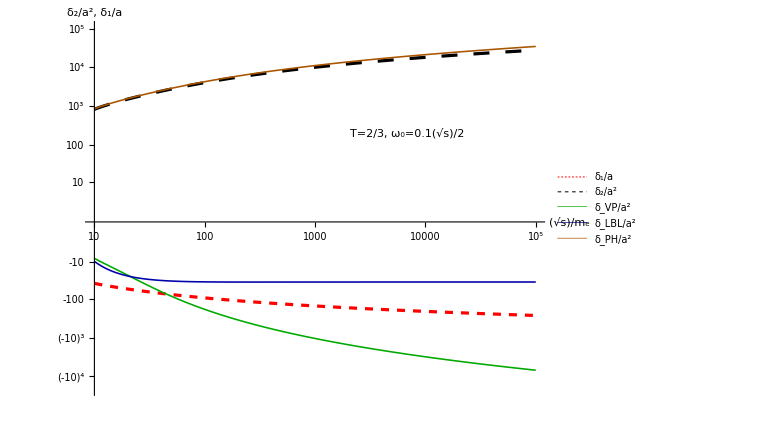

```mathematica
ncalc=Evaluate[{delta1exact/anum,δ2trun,Coefficient[δ2trun,nf]/.Lbl->0,Coefficient[δ2trun,Lbl],δ2trun/.{nf->0,Lbl->0}}/.{nf->1,Lbl->1}/.{log2ω0->Log[1/10],lmm->Log[1/x^2]}/.m->1/x/.T->2/3];
pl6=Plot[ncalc,{x,10,10^5},PlotRange->{{10,10^5},{-2 10^4,10^5}},ScalingFunctions->{"Log",{Sign[#] Log[1+Abs[#]]&,Sign[#]*(Exp[Abs[#]]-1)&}},PlotStyle->{{Red,Dashing[0.01],Thickness[0.004]},{Black,Dashing[0.02],Thickness[0.004]},{Darker[Green],Thickness[0.002]},{Darker[Blue],Thickness[0.002]},{Darker[Orange],Thickness[0.002]}},AxesLabel->{Style["(√s)/m_e",Medium,Bold],Style["δ_2/a^2, δ_1/a",Large,Medium]},PlotLegends->Placed[LineLegend[{Style["δ_1/a",FontFamily->"Times"],Style["δ_2/a^2",FontFamily->"Times"],Style["δ_VP/a^2",FontFamily->"Times"],Style["δ_LBL/a^2",FontFamily->"Times"],Style["δ_PH/a^2",FontFamily->"Times"]}],{0.90,0.75}],Ticks->{Automatic,Join@@Table[If[Abs[q]≥3,{w 10^q,"\!\(\*SuperscriptBox[\("<>ToString[w*10]<>"\), \("<>ToString[q]<>"\)]\)"},{w 10^q,ToString[w 10^q]}],{q,1,5},{w,{1,-1}}]}];
Show[pl6,Epilog->{Inset[Framed[Style["T=2/3, ω_0=0.1(√s)/2",14],Background->White],Scaled[{0.7, 0.7}]]}]
```

## Numerical comparison with ee->γγ^* https://arxiv.org/abs/2308.09479

```mathematica
(* Here we perform a comparison by projecting both amplitudes onto a test set of tensor structures. To perform this comparison we use LiteRed2,as well as packages that allow to calculate traces of gamma matrices and the numerical calculation of Goncharov's polylogarythms, we use GMatrices and REPLica*)
```

#### Load packages

```mathematica
<<LiteRed2`;
<<RNL`GMatrices`;
<<REPLica`;
SetDim[d];
Declare[{l1,l2,p1,p2,k1,k2},Vector,{mm,t,m,u,lmm,T,U,log2ω0},Number,{α,β,μ,ν,σ,λ},VectorIndex];
k2rule=k2:>p1+p2-k1;
SetConstraints[{p1,p2,k1,k2},
sp[p1]=sp[p2]=m^2;sp[k1]=sp[p1+p2-k1]=0;sp[p1+p2]=1;sp[p1-k1]=m^2-T;sp[k2,k2]=0;sp[k1,k2]=1/2;sp[k2,p2]=T/2;sp[k2,p1]=(1-T)/2;
];
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Wed 23 Apr 2025 16:49:08
Read from:/home/slava/.Mathematica/Applications/LiteRed2/Source/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

RNL/GMatrices.wl

Input file hash: 203663465247136170399747680750698142610

****************GMatrices v1.********************
Author:Roman N.Lee, Budker Institute of Nuclear Physics,Novosibirsk.
GMatrices package defines types for Dirac's gamma-matrices.
See ?GMatrices`* for a list of functions.

Interface to several REPL CAS.
Written by Roman Lee in 2020-- for private needs.

Executing
k1·k1=0;k1·k2=1/2;k1·p1=T/2;k1·p2=(1-T)/2;k2·k2=0;k2·p1=(1-T)/2;k2·p2=T/2;p1·p1=m^2;p1·p2=1/2-m^2;p2·p2=m^2;

#### Load hard amplitudes

```mathematica
(* Load Hard amplitudes Eq.(2.35) *)
{H0,H1,H2}=Get["Hkn/Hkn."<>ToString[#]]&/@Range[0,2];
(*Load Hard amplitudes from https://arxiv.org/abs/2308.09479 *)
{Hnarxiv0,Hnarxiv1,Hnarxiv2}=Get["gammastar/Hn/Hn.smallqq."<>ToString[#]]&/@Range[0,2];
```

Born massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s).

One-loop hard massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s), lmm=Log[m^2], ipi=I*π.

Two-loop hard massive invariant amplitudes.
 Format - double array of invariant amplitude number and m-series coefficient.
 Series starts from m^0.
 Notations: T=m_e^2/s, m=m_e/(√s), lmm=Log[m^2], ipi=I*π.
 nf=1 and Lbl=1 are flags.

#### Defining set of basis tensors

```mathematica
Pm=p1-p2;
Km=k1-k2;
ks={k1,k2};
(Subscript[g, μ,ν])_⊥:=(Subscript[g, μ,ν]-(Subscript[k1, μ] Subscript[k2, ν])/(k1·k2));
(SubIndex[p:Alternatives@@ks,ind_])_⊥:=Subscript[p, ind]-(SubIndex[Pm,ind]k1·k2)/((Complement[ks,{p}][[1]])·Pm);
(SubIndex[GMatrix,ind_])_⊥:=SubIndex[GMatrix,ind]-If[ind===ν,GHat[k1]SubIndex[k2,ind],GHat[k2]SubIndex[k1,ind]]/(k1·k2);
tensors=Join[GIdentity*{(Subscript[g, μ,ν])_⊥,(Subscript[k2, ν])_⊥(Subscript[k1, μ])_⊥},{((Subscript[γ, ν])_⊥(Subscript[k1, μ])_⊥-(Subscript[γ, μ])_⊥(Subscript[k2, ν])_⊥)sp[p1,k1-k2],OverHat[Km](Subscript[g, μ,ν])_⊥sp[p1,k1-k2],OverHat[Km](Subscript[k2, ν])_⊥(Subscript[k1, μ])_⊥sp[p1,k1-k2]},{((Subscript[γ, ν])_⊥.(Subscript[γ, μ])_⊥-(Subscript[γ, μ])_⊥.(Subscript[γ, ν])_⊥)sp[p1,k1-k2],sp[p1,k1-k2]((OverHat[Km].(Subscript[γ, ν])_⊥-(Subscript[γ, ν])_⊥.OverHat[Km])(Subscript[k1, μ])_⊥+(OverHat[Km].(Subscript[γ, μ])_⊥-(Subscript[γ, μ])_⊥.OverHat[Km])(Subscript[k2, ν])_⊥+(4 (m^2-T+T^2))/(-1+2 T)^2((Subscript[γ, ν])_⊥.(Subscript[γ, μ])_⊥-(Subscript[γ, μ])_⊥.(Subscript[γ, ν])_⊥))},{((Subscript[γ, μ])_⊥.OverHat[Km].(Subscript[γ, ν])_⊥-(Subscript[γ, ν])_⊥.OverHat[Km].(Subscript[γ, μ])_⊥)+(4 m)/(-1+2 T)^2((Subscript[γ, ν])_⊥.(Subscript[γ, μ])_⊥-(Subscript[γ, μ])_⊥.(Subscript[γ, ν])_⊥)sp[p1,k1-k2]}]/.Subscript[q__]:>SubIndex[q];
pr1=g^(ν,β)-(k1^ν*k2^β+k2^ν*k1^β)/(k1·k2);
pr2=g^(μ,α)-(k1^μ*k2^α+k2^μ*k1^α)/(k1·k2);
```

#### Projection onto test tensor set

```mathematica
(*Some test tensor structures to compare*)
```

```mathematica
tensorstest=Join[GIdentity*{Subscript[g, μ,ν],(Subscript[p1, μ]*Subscript[p2, ν]+Subscript[p1, ν]*Subscript[p2, μ])/2,(Subscript[p1, μ]*Subscript[p2, ν]-Subscript[p1, ν]*Subscript[p2, μ])/2,Subscript[p2, μ]*Subscript[p2, ν],Subscript[p1, μ]*Subscript[p1, ν]},{(Subscript[γ, μ] Subscript[p1, ν]+Subscript[γ, ν] Subscript[p1, μ])/2,(Subscript[γ, μ] Subscript[p1, ν]-Subscript[γ, ν] Subscript[p1, μ])/2,(Subscript[γ, μ] Subscript[p2, ν]+Subscript[γ, ν] Subscript[p2, μ])/2,(Subscript[γ, μ] Subscript[p2, ν]-Subscript[γ, ν] Subscript[p2, μ])/2},OverHat[k1]{Subscript[g, μ,ν],(Subscript[p1, μ]*Subscript[p2, ν]+Subscript[p1, ν]*Subscript[p2, μ])/2,(Subscript[p1, μ]*Subscript[p2, ν]-Subscript[p1, ν]*Subscript[p2, μ])/2,Subscript[p2, μ]*Subscript[p2, ν],Subscript[p1, μ]*Subscript[p1, ν]},1/2{Subscript[γ, μ].Subscript[γ, ν]-Subscript[γ, ν].Subscript[γ, μ]},{((OverHat[k1].Subscript[γ, μ])*Subscript[p1, ν]+(OverHat[k1].Subscript[γ, ν])*Subscript[p1, μ])/2,((OverHat[k1].Subscript[γ, μ])*Subscript[p1, ν]-(OverHat[k1].Subscript[γ, ν])*Subscript[p1, μ])/2,((OverHat[k1].Subscript[γ, μ])*Subscript[p2, ν]+(OverHat[k1].Subscript[γ, ν])*Subscript[p2, μ])/2,((OverHat[k1].Subscript[γ, μ])*Subscript[p2, ν]-(OverHat[k1].Subscript[γ, ν])*Subscript[p2, μ])/2},1/6{Subscript[γ, μ].OverHat[k1].Subscript[γ, ν]-Subscript[γ, ν].OverHat[k1].Subscript[γ, μ]}];
dummyconst=Table[Symbol["c"<>ToString[q]],{q,1,Length@tensorstest}];
Declare[Evaluate@dummyconst,Number];
```

```mathematica
(* tensor structures from https://arxiv.org/abs/2308.09479 *)
```

```mathematica
tensorsarxiv={(Subscript[p1, μ]/(1-T)-Subscript[k1, μ]/(T+U))*(Subscript[γ, σ]-(2GHat[k1] Subscript[p1, σ])/T),(Subscript[p2, μ]/(1-U)-Subscript[k1, μ]/(T+U))*(Subscript[γ, σ]-(2GHat[k1] Subscript[p2, σ])/U),(Subscript[p2, μ]/(1-U)-Subscript[k1, μ]/(T+U))*(Subscript[γ, σ]-(2GHat[k1] Subscript[p1, σ])/T),(Subscript[p1, μ]/(1-T)-Subscript[k1, μ]/(T+U))*(Subscript[γ, σ]-(2GHat[k1] Subscript[p2, σ])/U),-Subscript[p2, μ]/(1-U)(Subscript[γ, σ]-(2GHat[k1] Subscript[p1, σ])/T)+Subscript[p1, μ]/(1-T)(Subscript[γ, σ]-(2GHat[k1] Subscript[p2, σ])/U)+Subscript[γ, μ](Subscript[p1, σ]/T-Subscript[p2, σ]/U),1/(T*U)(GHat[k1]*Subscript[g, μ,σ]-Subscript[γ, σ]*Subscript[k1, μ])+Subscript[p2, μ]/(U(1-U))(Subscript[γ, σ]-(2GHat[k1] Subscript[p1, σ])/T)+Subscript[p1, μ]/(T(1-T))(Subscript[γ, σ]-(2GHat[k1] Subscript[p2, σ])/U),(Subscript[γ, σ].GHat[k1].Subscript[γ, μ]-Subscript[γ, μ].GHat[k1].Subscript[γ, σ])/2+Subscript[p2, μ](T*Subscript[γ, σ]-2GHat[k1] Subscript[p1, σ])-Subscript[p1, μ](U*Subscript[γ, σ]-2GHat[k1] Subscript[p2, σ])+Subscript[γ, μ](U*Subscript[p1, σ]-T*Subscript[p2, σ])}/.U->(1-T)/.{σ->ν}/.SubIndex[q__]:>SupIndex[q]/.MetricTensor[List[],q__]:>MetricTensor[q,List[]];
```

```mathematica
(* Projection structures from https://arxiv.org/abs/2308.09479 on test structures*)
```

```mathematica
inprodarxiv=LFDistribute[(DummyEliminate[#]&/@(FORMTraces[gTrace[pr1*pr2*GReduce[((1/2 (-GIdentity*m+OverHat[p2])).(#).(1/2 (GIdentity*m+OverHat[p1]))).((tensorstest.dummyconst/.{μ->α,ν->β})/.sp[q_,w_]:>LFDistribute[sp[q,w]])]]]&/@tensorsarxiv))];
```

```mathematica
amparxiv=(((a^2 Hnarxiv2+a Hnarxiv1+Hnarxiv0)/.Log[mm]->lmm/.Log[qq]->lqq).inprodarxiv)/.d->4/.m->0;
```

```mathematica
(* Projection structures from this work on test structures *)
```

```mathematica
inprod=LFDistribute[(DummyEliminate[#]&/@(FORMTraces[gTrace[pr1*pr2*GReduce[((1/2 (-GIdentity*m+OverHat[p2])).(#).(1/2 (GIdentity*m+OverHat[p1]))).((tensorstest.dummyconst/.{μ->α,ν->β})/.sp[q_,w_]:>LFDistribute[sp[q,w]])]]]&/@tensors))];
```

```mathematica
(* To get true hard amplitudes ℋ we need to multiply on inverse matrix D from Eq.(2.30)*)
```

```mathematica
amp=(a^2 H2[[All,1]]+a H1[[All,1]]+ H0[[All,1]]).Factor[Inverse[matrixD].inprod/.m->0/.d->4]/.ipi->(I*π);
```

#### Numerical calculation of difference

```mathematica
(* Numerical difference an any point T and any accuracy. *)
```

```mathematica
ncalc=Chop@Simplify[(GinshN[amparxiv/.{LbL->Lbl,Nf->nf}/.T->#,30]+N[amp/.T->#,30])&@(3/7)]
```

0